```mathematica
SetDirectory[NotebookDirectory[]]
rawTuples=Import["parameter_sweep/tuple_names.csv","Table"];
rawEIR=Import["parameter_sweep/EIR_sweep.csv","Table"];
```

/Users/chipdelmal/Documents/School/Research/VCOM/OtherRoutines

```mathematica
{head,tuples,eir}={StringSplit[rawTuples[[1]],","][[1]],((ToExpression/@(StringSplit[#,","]))&/@rawTuples[[2;;All]])[[All,1]],(ToExpression/@rawEIR)[[All,1]]};
head2=Append[head,"EIR"];
data=Transpose[{tuples,eir}];
data[[1]]
```

{{100,1,0,20,0,20,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},100.}

```mathematica
Transpose[{head,tuples[[100]]}]//Grid;
```

```mathematica
coverages=Range[0,1,.2]
```

{0.,0.2,0.4,0.6,0.8,1.}

```mathematica
controlVct=Flatten[{Range[3,tuples[[1]]//Length,2]}];
inOuts={#[[controlVct]]&/@tuples,eir}//Transpose;
Grid[{{
ArrayPlot[inOuts[[All,1]],ImageSize->1000,Frame->None,AspectRatio->5,ColorFunction->"TemperatureMap",PlotLegends->Placed[Automatic,Left],PlotRangePadding->0],
ArrayPlot[Transpose[{inOuts[[All,2]]}],ImageSize->1000,Frame->None,AspectRatio->5,ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRangePadding->0]
}}];
Export["CoolAtari.png",%,ImageSize->2000,ImageResolution->100]
```

CoolAtari.png

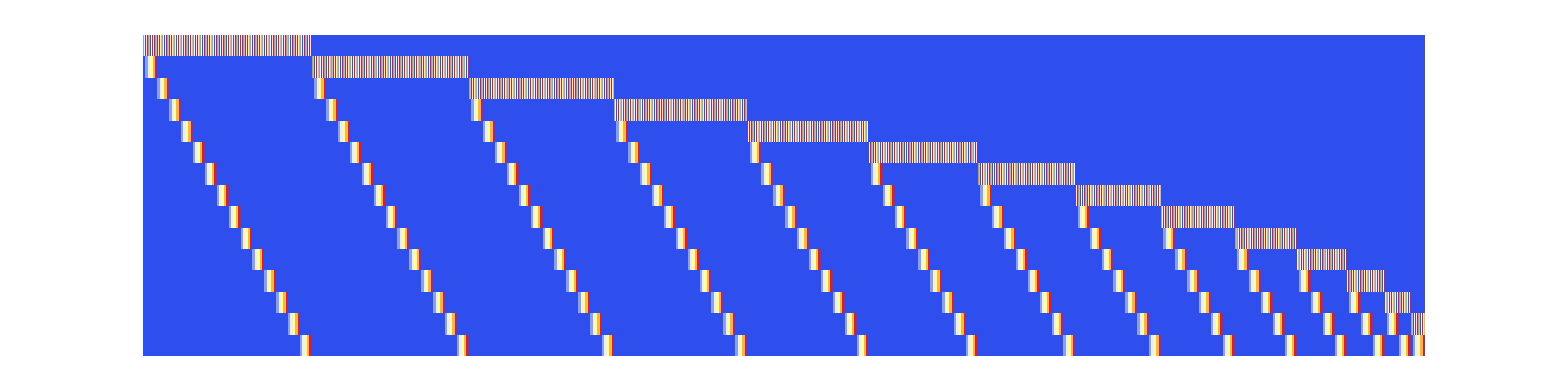
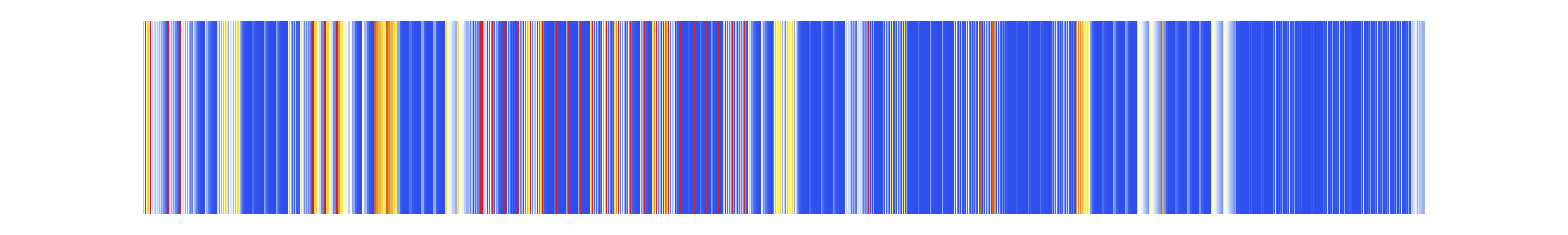

CoolAtari2.png

```mathematica
color="TemperatureMap";
Grid[{
{ArrayPlot[Transpose[inOuts[[All,1]]],ImageSize->2000,Frame->None,AspectRatio->.25,ColorFunction->color,PlotLegends->Placed[Automatic,Top],PlotRangePadding->0]},
{ArrayPlot[{inOuts[[All,2]]},ImageSize->2000,Frame->None,AspectRatio->.15,ColorFunction->color,PlotLegends->Placed[Automatic,Bottom],PlotRangePadding->0]}
}]
Export["CoolAtari2.png",%,ImageSize->2000,ImageResolution->300]
```

```mathematica
{covTotal,eirValue}={.6,1};
filtered=Cases[inOuts,{a_,b_}/;Total[a]≤covTotal&&b≤eirValue];
Grid[Flatten[{{Append[head[[controlVct]],"EIR"]},Flatten/@filtered},1],Background->{None,{LightBlue}}]
Export["table.png",%]
```

OVIcov | FOGcov | LARcov | BIOcov | SREcov | IRScov | ITNcov | ECScov | ECTcov | HOUcov | OBTcov | SPRcov | PPMcov | ATSBcov | SSPcov | EIR
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0.2 | 0 | 0 | 0 | 0 | 0.657565
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.4 | 0 | 0 | 0 | 0 | 0.694335
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0.718295
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0.2 | 0 | 0 | 0 | 0.694335
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.4 | 0 | 0 | 0 | 0.657565
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0.2 | 0 | 0 | 0.694335
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0.4 | 0 | 0 | 0.657565
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0.594031

table.png